```mathematica
Needs["Wolfram`QuantumFramework`"]
```

```mathematica
mbSpherical[z_,k_]:=Module[{m},m=MatrixExp[(I ω)/2(Sin[θ]Cos[ϕ]PauliMatrix[1]+Sin[θ]Sin[ϕ]PauliMatrix[2]+Cos[θ]PauliMatrix[3])].{z,1};m[[1]]/m[[2]]/.ω->(k Pi)/6/.θ->0/.ϕ->Pi/3]
```

```mathematica
bloch[x_]:=Table[Tr[PauliMatrix[i].Normal[x["State"]]],{i,1,3}]
```

```mathematica
ψi=QuantumState[{Cos[θ/2],ⅇ^(ⅈ ϕ)Sin[θ/2]}];
```

```mathematica
tx=Texture[Rasterize[ComplexPlot[mbSpherical[Cot[Re[w]/2] Exp[I Im[w]],1],{w,0,π+2Pi I},Sequence[ColorFunction->"None",Frame->False,PlotRangePadding->0,BoundaryStyle->None]],ImageResolution->100]]
```

Texture[-Graphics-]

```mathematica
With[{bloch=ψi["BlochCartesianCoordinates"]},ParametricPlot3D[bloch,{θ,0,π},{ϕ,0,2π},PlotLabel->"Bloch Sphere, initial",PlotStyle->tx,TextureCoordinateFunction->({#4,#3}&)]]
```

-Graphics3D-

```mathematica
Manipulate[With[{q1=QuantumChannel[{#,p}][QuantumState["+"]]["BlochPlot"]/.Sphere[_]:>Nothing,bloch=QuantumChannel[{#,p}][ψi]//bloch,q2=(QuantumState["+"])["BlochPlot"]/.Sphere[_]:>Nothing/.Ket[x_]:>" "/.Red->Green},Show[ParametricPlot3D[{},{θ,0,π},{ϕ,0,2π},PlotStyle->tx,TextureCoordinateFunction->({#4,#3}&),PlotRange->{{-1,1},{-1,1},{-1,1}},PlotLabel->#],q1,q2,PlotRange->All]]&/@{"BitFlip","PhaseFlip","BitPhaseFlip","Depolarizing","AmplitudeDamping","PhaseDamping"}//Partition[#,3]&//GraphicsGrid,{{p,0.35},0,2}]
```

```mathematica
Manipulate[With[{q1=QuantumChannel[{#,p}][QuantumState["+"]]["BlochPlot"]/.Sphere[_]:>Nothing,bloch=QuantumChannel[{#,p}][ψi]//bloch,q2=QuantumState["+"]["BlochPlot"]/.Sphere[_]:>Nothing/.Ket[x_]:>" "/.Red->Green},Show[ParametricPlot3D[bloch,{θ,0,π},{ϕ,0,2π},PlotStyle->tx,TextureCoordinateFunction->({#4,#3}&),PlotRange->{{-1,1},{-1,1},{-1,1}},PlotLabel->#],q1,q2,PlotRange->All]]&/@{"BitFlip","PhaseFlip","BitPhaseFlip","Depolarizing","AmplitudeDamping","PhaseDamping"}//Partition[#,3]&//GraphicsGrid,{{p,0.35},0,2}]
```

```mathematica
e[x_,y_]:=SparseArray[{{x,y}->1},{d,d}]//Normal
e[a_]:=Partition[Array[KroneckerDelta[#,a]&,d^2],d]
```

```mathematica
mu[i_,j_]:=SparseArray[{i,j}->1,{d,d}];
```

```mathematica
QuantumOperator[PauliMatrix[1]+I PauliMatrix[2]]["Matrix"]//Normal//MatrixForm
```

(0 | 2
0 | 0)

## 从Channel到蔡氏矩阵：以比特翻转为例

```mathematica
d=2;
kr=KroneckerProduct;
aj=ConjugateTranspose;
```

```mathematica
ϵ[x_]:=Simplify[(QuantumChannel[{"AmplitudeDamping",q}][QuantumState[x]])["DensityMatrix"]//Normal,1>q>0]
```

```mathematica
ϵ[x_]:=Simplify[(QuantumChannel[{"Depolarizing",q}][QuantumState[x]])["DensityMatrix"]//Normal,1>q>0]
mu[i_,j_]:=SparseArray[{i,j}->1,{d,d}];
```

```mathematica
ϵ[x_]:=Simplify[(QuantumChannel[{"BitPhaseFlip",q}][QuantumState[x]])["DensityMatrix"]//Normal,1>q>0]
mu[i_,j_]:=SparseArray[{i,j}->1,{d,d}];
```

```mathematica
ϵ[x_]:=Simplify[(QuantumChannel[{"BitFlip",q}][QuantumState[x]])["DensityMatrix"]//Normal,1>q>0]
mu[i_,j_]:=SparseArray[{i,j}->1,{d,d}];
```

```mathematica
ϵ[x_]:=γ {{0,0},{0,1}}.x.{{0,0},{0,1}}+γ {{1,0},{0,0}}.x.{{1,0},{0,0}}+(1-2γ)x
```

```mathematica
ϵ[IdentityMatrix[2]]
ϵ[PauliMatrix[3]]
```

{{1,0},{0,1}}

{{1-2 q,0},{0,-1+2 q}}

```mathematica
choiMatrix[ϵ_]:=Table[ϵ[mu[i,j]],{i,d},{j,d}]/d//SparseArray(*从Channel到蔡氏矩阵*)
```

```mathematica
cmb=choiMatrix[ϵ]//Normal
```

{{{{(1-γ)/2,0},{0,0}},{{0,1/2 (1-2 γ)},{0,0}}},{{{0,0},{1/2 (1-2 γ),0}},{{0,0},{0,(1-γ)/2}}}}

```mathematica
ArrayFlatten[cmb]
```

{{(1-γ)/2,0,0,1/2 (1-2 γ)},{0,0,0,0},{0,0,0,0},{1/2 (1-2 γ),0,0,(1-γ)/2}}

```mathematica
ArrayFlatten[cmb]//Eigenvalues
```

{0,0,1/2 (2-3 γ),γ/2}

```mathematica
QuantumChannel[{"BitFlip",p}]["Properties"]
```

{Amplitude,Amplitudes,Arity,Association,Basis,BasisEffects,BasisMaps,BasisStates,Bend,BendDual,Bipartition,Chop,CircuitDiagram,ComplexExpand,Computational,ComputationalQ,Conjugate,ConjugateTranspose,ControlOrder,Dagger,Decompose,DecomposeWithAmplitudes,DecomposeWithProbabilities,DensityMatrix,Diagonalize,Diagram,Dimension,Dimensions,Disentangle,Double,Dual,Eigenstates,Eigensystem,Eigenvalues,Eigenvectors,ElementAssociation,ElementDimension,ElementDimensions,ElementNames,Elements,Entropy,FinalParameters,FirstInputQudit,FirstOutputQudit,Formula,FullArity,FullInputOrder,FullInputQudits,FullOrder,FullOutputOrder,FullOutputQudits,FullQudits,FullSimplify,HasInputQ,HermitianQ,InitialParameters,Input,InputBasis,InputDimension,InputDimensions,InputElementDimension,InputElementDimensions,InputElementNames,InputElements,InputMatrix,InputNameDimension,InputNameDimensions,InputOrder,InputOrderQuditMapping,InputQuditOrder,InputQudits,InputRank,InputSize,InputTensor,Inverse,Kind,Label,LabelHead,LastInputQudit,LastOutputQudit,LogicalEntropy,Matrix,MatrixDimensions,MatrixElementDimensions,MatrixNameDimensions,MatrixQ,MatrixRepresentation,MatrixState,MaxArity,Mixed,MixedStateQ,NameDimensions,Names,Norm,NormalElementNames,NormalizedAmplitudes,NormalizedDensityMatrix,NormalizedOperator,NormalizedProjector,NormalizedQ,NormalizedState,NormalizedStateVector,NumberQ,NumericQ,Operator,Order,Ordered,OrderedFormula,OrderedInput,OrderedMatrix,OrderedMatrixRepresentation,OrderedOutput,OrderedTensor,OrderedTensorRepresentation,OrthogonalElements,Output,OutputBasis,OutputDimension,OutputDimensions,OutputElementDimension,OutputElementDimensions,OutputElementNames,OutputElements,OutputMatrix,OutputNameDimension,OutputNameDimensions,OutputOrder,OutputOrderQuditMapping,OutputQuditOrder,OutputQudits,OutputRank,OutputSize,OutputTensor,ParameterArity,Parameters,ParameterSpec,PauliDecompose,Physical,PhysicalQ,Picture,PrimeBasis,Probabilities,Probability,Projector,Projectors,Pure,PureStateQ,Purify,Purity,QuantumOperator,QuditBasis,QuditOrder,Qudits,Range,Rank,Reverse,ReverseInput,ReverseOutput,Scalar,SchmidtBasis,SchmidtDecompose,Shift,Simplify,Size,Sort,SortInput,SortOutput,SpectralBasis,Split,SplitDual,State,StateMatrix,StateTensor,StateType,StateVector,TargetArity,TargetOrder,Tensor,TensorDimensions,TensorRepresentation,TensorReverseInput,TensorReverseOutput,Trace,TraceDimensions,TraceNorm,TraceOrder,TracePreservingQ,TraceQudits,Transpose,Type,Unbend,UniformBasis,UnitaryQ,UnknownQ,Unpurify,UnstackInput,UnstackOutput,VectorQ,VectorState,VonNeumannEntropy,Weights}

## 从蔡氏矩阵到Kraus算符

```mathematica
choi2ks[choi_]:=Module[{d,egv,u0,β,χ,u,A,kraus,e,ϵ
},d=Dimensions[choi][[1]];ϵ=d Sum[Tr[ArrayFlatten[choi].kr[mu[i,j],Transpose[#]]] mu[j,i],{i,d},{j,d}]&;e[x_,y_]:=SparseArray[{{x,y}->1},{d,d}]//Normal;
e[a_]:=Partition[Array[KroneckerDelta[#,a]&,d^2],d];β=ArrayFlatten[TensorTranspose[Table[Tr[ConjugateTranspose[e[j]].e[l].e[k].aj[e[p]]],{j,d^2},{l,d^2},{k,d^2},{p,d^2}],{1,2,3,4}]];
χ=Partition[LinearSolve[β,Flatten[Table[Tr[aj[e[pp]].ϵ[e[ll]]],{pp,d^2},{ll,d^2}](*如果pp改为p会导致错误，因为p是Kraus算符的参数*)]],d^2];{egv,u0}=Eigensystem[χ]//Simplify;
u=#/Norm[#]&/@u0;
A=√DiagonalMatrix[egv].u//FullSimplify;
kraus=A.Table[e[i],{i,d^2}]/.Table[0,{i,d},{j,d}]->Nothing//Chop](*从蔡氏矩阵到一组Kraus算符*)
```

```mathematica
c2k=choi2ks;
```

```mathematica
choi=choiMatrix[ϵ]//Normal;
```

```mathematica
krs=choi2ks[choi]//Simplify[#,Γ>0&&t>0]&
```

{{{√(1-p),0},{0,√(1-p)}},{{0,√p},{√p,0}}}

### 讨论蔡氏矩阵的本征值和本征态

```mathematica
Tr[aj[krs[[1]]].krs[[2]]]
Tr[aj[krs[[1]]].krs[[1]]]//Simplify[#,Γ>0&&t>0]&
Tr[aj[krs[[2]]].krs[[2]]]//Simplify[#,Γ>0&&t>0]&
```

0

2 √(1-p) Conjugate[√(1-p)]

2 √p Conjugate[√p]

```mathematica
egs=Eigensystem[ArrayFlatten@choi]//FullSimplify
```

{{0,0,1-p,p},{{-1,0,0,1},{0,-1,1,0},{1,0,0,1},{0,1,1,0}}}

```mathematica
krsp=Partition[#,2]&/@egs[[2]]
```

{{{-1,0},{0,1}},{{0,-1},{1,0}},{{1,0},{0,1}},{{0,1},{1,0}}}

```mathematica
e1[x_]:=Sum[krsp[[i]].x.aj[krsp[[i]]],{i,4}]
```

```mathematica
choip=choiMatrix[e1]//ArrayFlatten//Normal//Simplify[#,Γ>0&&t>0]&
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
choi//ArrayFlatten//Normal//FullSimplify[#,Γ>0&&t>0]&
```

{{(1-p)/2,0,0,(1-p)/2},{0,p/2,p/2,0},{0,p/2,p/2,0},{(1-p)/2,0,0,(1-p)/2}}

```mathematica
(1/(1-ⅇ^(-t Γ))choi//ArrayFlatten//Normal//FullSimplify[#,Γ>0&&t>0]&)-choip//Simplify
```

{{-1-(ⅇ^(t Γ) (-1+p))/(2 (-1+ⅇ^(t Γ))),0,0,-(ⅇ^(t Γ) (-1+p))/(2 (-1+ⅇ^(t Γ)))},{0,-1+1/2 (1+1/(-1+ⅇ^(t Γ))) p,1/2 (1+1/(-1+ⅇ^(t Γ))) p,0},{0,1/2 (1+1/(-1+ⅇ^(t Γ))) p,-1+1/2 (1+1/(-1+ⅇ^(t Γ))) p,0},{-(ⅇ^(t Γ) (-1+p))/(2 (-1+ⅇ^(t Γ))),0,0,-1-(ⅇ^(t Γ) (-1+p))/(2 (-1+ⅇ^(t Γ)))}}

## 几种典型信道的Kraus算符

```mathematica
expKrs[name_]:=Module[{d,egv,u0,β,χ,u,A,kraus,e,ϵ
},d=2;ϵ[x_]:=Simplify[(QuantumChannel[{name,p}][QuantumState[x]])["DensityMatrix"]//Normal,1>p>0];e[x_,y_]:=SparseArray[{{x,y}->1},{d,d}]//Normal;
e[a_]:=Partition[Array[KroneckerDelta[#,a]&,d^2],d];
β=ArrayFlatten[TensorTranspose[Table[Tr[ConjugateTranspose[e[j]].e[l].e[k].aj[e[p]]],{j,d^2},{l,d^2},{k,d^2},{p,d^2}],{1,2,3,4}]];
χ=Partition[LinearSolve[β,Flatten[Table[Tr[aj[e[pp]].ϵ[e[ll]]],{pp,d^2},{ll,d^2}](*如果pp改为p会导致错误，因为p是Kraus算符的参数*)]],d^2];{egv,u0}=Eigensystem[χ]//Simplify;
u=#/Norm[#]&/@u0;
A=√DiagonalMatrix[egv].u//FullSimplify;
kraus=A.Table[e[i],{i,d^2}]/.Table[0,{i,d},{j,d}]->Nothing//Chop;Row[{name," ",MatrixForm/@kraus}]]
```

```mathematica
expKrs/@{"BitFlip","PhaseFlip","BitPhaseFlip","Depolarizing","AmplitudeDamping","PhaseDamping"}//Simplify[#,0<p<1]&//Column
```

BitFlip {(√(1-p) | 0
0 | √(1-p)),(0 | √p
√p | 0)}
PhaseFlip {(√(1-p) | 0
0 | √(1-p)),(-√p | 0
0 | √p)}
BitPhaseFlip {(√(1-p) | 0
0 | √(1-p)),(0 | -√p
√p | 0)}
Depolarizing {(1/2 √(4-3 p) | 0
0 | 1/2 √(4-3 p)),(-(√p)/2 | 0
0 | (√p)/2),(0 | 0
(√p)/(√2) | 0),(0 | (√p)/(√2)
0 | 0)}
AmplitudeDamping {(1 | 0
0 | √(1-p)),(0 | √p
0 | 0)}
PhaseDamping {(-(√(1-√(1-p)))/(√2) | 0
0 | (√(1-√(1-p)))/(√2)),((√(1+√(1-p)))/(√2) | 0
0 | (√(1+√(1-p)))/(√2))}

相位阻尼和相位反转一样

```mathematica
expKrs1[name_]:=Module[{d,egv,u0,β,χ,u,A,kraus,e,ϵ
},d=2;ϵ[x_]:=Simplify[(QuantumChannel[{name,p}][QuantumState[x]])["DensityMatrix"]//Normal,1>p>0];e[x_,y_]:=SparseArray[{{x,y}->1},{d,d}]//Normal;
e[a_]:=Partition[Array[KroneckerDelta[#,a]&,d^2],d];
β=ArrayFlatten[TensorTranspose[Table[Tr[ConjugateTranspose[e[j]].e[l].e[k].aj[e[p]]],{j,d^2},{l,d^2},{k,d^2},{p,d^2}],{1,2,3,4}]];
χ=Partition[LinearSolve[β,Flatten[Table[Tr[aj[e[pp]].ϵ[e[ll]]],{pp,d^2},{ll,d^2}](*如果pp改为p会导致错误，因为p是Kraus算符的参数*)]],d^2];{egv,u0}=Eigensystem[χ]//Simplify;
u=#/Norm[#]&/@u0;
A=√DiagonalMatrix[egv].u//FullSimplify;
kraus=A.Table[e[i],{i,d^2}]/.Table[0,{i,d},{j,d}]->Nothing//Chop]
```

```mathematica
kraus1=expKrs1["PhaseDamping"]
Sum[aj@kraus1[[i]].kraus1[[i]],{i,Length[kraus1]}]//FullSimplify//Simplify[#,0<p<1]&
```

{{{-(√(1-√(1-p)))/(√2),0},{0,(√(1-√(1-p)))/(√2)}},{{(√(1+√(1-p)))/(√2),0},{0,(√(1+√(1-p)))/(√2)}}}

{{1,0},{0,1}}

## 几种典型信道的Bloch向量仿射变换矩阵

```mathematica
blochaffin[name_]:=Module[{ϵ},ϵ[x_]:=Simplify[(QuantumChannel[{name,p}][QuantumState[x]])["DensityMatrix"]//Normal,1>p>0];Row[{name,MatrixForm@Table[Tr[PauliMatrix[i].ϵ[PauliMatrix[j]/2]],{i,4},{j,4}]}]]
```

```mathematica
blochaffin1[name_]:=Module[{ϵ},ϵ[x_]:=Simplify[(QuantumChannel[{name,p}][QuantumState[x]])["DensityMatrix"]//Normal,1>p>0];Table[Tr[PauliMatrix[i].ϵ[PauliMatrix[j]/2]],{i,4},{j,4}]]
```

```mathematica
blochaffin/@{"BitFlip","PhaseFlip","BitPhaseFlip","Depolarizing","AmplitudeDamping","PhaseDamping"}//Simplify[#,0<p<1]&//Column
```

BitFlip(1 | 0 | 0 | 0
0 | 1-2 p | 0 | 0
0 | 0 | 1-2 p | 0
0 | 0 | 0 | 1)
PhaseFlip(1-2 p | 0 | 0 | 0
0 | 1-2 p | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)
BitPhaseFlip(1-2 p | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1-2 p | 0
0 | 0 | 0 | 1)
Depolarizing(1-p | 0 | 0 | 0
0 | 1-p | 0 | 0
0 | 0 | 1-p | 0
0 | 0 | 0 | 1)
AmplitudeDamping(√(1-p) | 0 | 0 | 0
0 | √(1-p) | 0 | 0
0 | 0 | 1-p | p
0 | 0 | 0 | 1)
PhaseDamping(√(1-p) | 0 | 0 | 0
0 | √(1-p) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## 从信道到Kraus算符更多例子

#### 算例1

```mathematica
ϵ[r_]:={{ⅇ^(-t Γ) r⟦1,1⟧,ⅇ^(-(t Γ)/2) r⟦1,2⟧},{ⅇ^(-(t Γ)/2) r⟦2,1⟧,(1-ⅇ^(-t Γ)) r⟦1,1⟧+r⟦2,2⟧}}(*末态*)
```

```mathematica
d=2;(*Hilbert空间的维度*)
β=ArrayFlatten[TensorTranspose[Table[Tr[aj[e[j]].e[l].e[k].SuperDagger[e[p]]],{j,d^2},{l,d^2},{k,d^2},{p,d^2}],{1,2,3,4}]];χ=Partition[LinearSolve[β,Flatten[Table[Tr[SuperDagger[e[p]].ϵ[e[l]]],{p,d^2},{l,d^2}]]],d^2];
{egv,u0}=Eigensystem[χ]//Simplify;
u=#/Norm[#]&/@u0;
A=√DiagonalMatrix[egv].u//FullSimplify;
kraus=A.Table[e[i],{i,d^2}]/.Table[0,{i,d},{j,d}]->Nothing(*Kraus算符*)
Sum[aj@kraus[[i]].kraus[[i]],{i,Length[kraus]}]//FullSimplify//MatrixForm(*检验正交归一关系*)
```

$Aborted

Set::shape: Lists {egv,u0} and Eigensystem[χ] are not the same shape.

√DiagonalMatrix[egv].u0.{{{1,0},{0,0}},{{0,1},{0,0}},{{0,0},{1,0}},{{0,0},{0,1}}}

Dot::dotsh: Tensors {{{1,0},{0,1},{0,0},{0,0}},{{0,0},{0,0},{1,0},{0,1}}} and {{{1,0},{0,0}},{{0,1},{0,0}},{{0,0},{1,0}},{{0,0},{0,1}}} have incompatible shapes.

ConjugateTranspose[u0].u0+ConjugateTranspose[√DiagonalMatrix[egv]].√DiagonalMatrix[egv]+{{{1,0},{0,1},{0,0},{0,0}},{{0,0},{0,0},{1,0},{0,1}}}.{{{1,0},{0,0}},{{0,1},{0,0}},{{0,0},{1,0}},{{0,0},{0,1}}}

#### 算例2

```mathematica
Clear[b]
```

```mathematica
d=4;
qc1=QuantumTensorProduct[Table[QuantumChannel[{a QuantumOperator["X"],b QuantumOperator["Z"]},QuantumBasis[2]],{i,2}]];
```

```mathematica
β=ArrayFlatten[TensorTranspose[Table[Tr[SuperDagger[e[p]].e[j].e[l].SuperDagger[e[k]]],{j,d^2},{l,d^2},{k,d^2},{p,d^2}],{2,3,4,1}]];
```

```mathematica
elist=(Normal[#["DensityMatrix"]]&/@Table[qc1[QuantumState[e[l],QuantumBasis[{2,2}]]],{l,d^2}]//Simplify);
χ=Partition[LinearSolve[β,Flatten[Table[Tr[SuperDagger[e[p]].elist[[l]]],{p,d^2},{l,d^2}]]],d^2];
{egv,u0}=Eigensystem[χ]//Simplify
u=#/Norm[#]&/@u0;
A=√DiagonalMatrix[egv].u//FullSimplify;
kraus=A.Table[e[i],{i,d^2}]/.Table[0,{i,d},{j,d}]->Nothing;
MatrixForm/@kraus
Sum[SuperDagger[kraus[[i]]].kraus[[i]],{i,Length[kraus]}]//FullSimplify//MatrixForm
```

{{0,0,0,0,0,0,0,0,0,0,0,0,4 a^2 Conjugate[a]^2,4 b^2 Conjugate[b]^2,4 a b Conjugate[a b],4 a b Conjugate[a b]},{{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0},{1,0,0,0,0,-1,0,0,0,0,-1,0,0,0,0,1},{0,-1,0,0,-1,0,0,0,0,0,0,1,0,0,1,0},{0,0,-1,0,0,0,0,1,-1,0,0,0,0,1,0,0}}}

{(0 | 0 | 0 | Abs[a]^2
0 | 0 | Abs[a]^2 | 0
0 | Abs[a]^2 | 0 | 0
Abs[a]^2 | 0 | 0 | 0),(Abs[b]^2 | 0 | 0 | 0
0 | -b Conjugate[b] | 0 | 0
0 | 0 | -b Conjugate[b] | 0
0 | 0 | 0 | Abs[b]^2),(0 | -√(a b Conjugate[a] Conjugate[b]) | 0 | 0
-√(a b Conjugate[a] Conjugate[b]) | 0 | 0 | 0
0 | 0 | 0 | √(a b Conjugate[a] Conjugate[b])
0 | 0 | √(a b Conjugate[a] Conjugate[b]) | 0),(0 | 0 | -√(a b Conjugate[a] Conjugate[b]) | 0
0 | 0 | 0 | √(a b Conjugate[a] Conjugate[b])
-√(a b Conjugate[a] Conjugate[b]) | 0 | 0 | 0
0 | √(a b Conjugate[a] Conjugate[b]) | 0 | 0)}

((Abs[a]^2+Abs[b]^2)^2 | 0 | 0 | 0
0 | (Abs[a]^2+Abs[b]^2)^2 | 0 | 0
0 | 0 | (Abs[a]^2+Abs[b]^2)^2 | 0
0 | 0 | 0 | (Abs[a]^2+Abs[b]^2)^2)

#### 算例3

```mathematica
d=4;
```

```mathematica
ϵ[r_]:=Block[{g},g[x_,y_]:=r[[x,y]];Sum[krs[[i]].Array[g,{d,d}].SuperDagger[krs[[i]]],{i,2}]]
```

```mathematica
β=ArrayFlatten[TensorTranspose[Table[Tr[SuperDagger[e[p]].e[j].e[l].SuperDagger[e[k]]],{j,d^2},{l,d^2},{k,d^2},{p,d^2}],{2,3,4,1}]];
```

```mathematica
qc3=QuantumChannel[{QuantumOperator[KroneckerProduct[1/(√2)PauliMatrix[0],PauliMatrix[1]],QuantumBasis[4]],QuantumOperator[KroneckerProduct[1/(√2)PauliMatrix[1],PauliMatrix[0]],QuantumBasis[4]]},QuantumBasis[4]];
```

```mathematica
elist=(Normal[#["DensityMatrix"]]&/@Table[qc3[QuantumState[e[l],QuantumBasis[4]]],{l,d^2}]//Simplify);
```

```mathematica
χ=Partition[LinearSolve[β,Flatten[Table[Tr[SuperDagger[e[p]].elist[[l]]],{p,d^2},{l,d^2}]]],d^2];
{egv,u0}=Eigensystem[χ]//Simplify;
u=#/Norm[#]&/@u0;
```

```mathematica
A=√DiagonalMatrix[egv].u;
kraus=Chop[A.Table[e[i],{i,d^2}]]/.Table[0,{i,d},{j,d}]->Nothing//Simplify;
```

```mathematica
MatrixForm/@kraus(*完美地得到了预期的Kraus*)
Sum[SuperDagger[kraus[[i]]].kraus[[i]],{i,Length[kraus]}]//FullSimplify//MatrixForm
```

{(0 | 1/(√2) | 0 | 0
1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 1/(√2)
0 | 0 | 1/(√2) | 0),(0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 1/(√2)
1/(√2) | 0 | 0 | 0
0 | 1/(√2) | 0 | 0)}

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

#### 算例4：在另一组基底下展开Kraus算符（单比特）

计算的channel与算例1相同

```mathematica
ϵ[r_]:={{ⅇ^(-t Γ) r⟦1,1⟧,ⅇ^(-(t Γ)/2) r⟦1,2⟧},{ⅇ^(-(t Γ)/2) r⟦2,1⟧,(1-ⅇ^(-t Γ)) r⟦1,1⟧+r⟦2,2⟧}}
ml=1/(√2){IdentityMatrix[2],PauliMatrix[1],-I PauliMatrix[2],PauliMatrix[3]};
et[i_]:=ml[[i]]
```

```mathematica
d=2;β=ArrayFlatten[TensorTranspose[Table[Tr[SuperDagger[e[p]].et[j].e[l].SuperDagger[et[k]]],{j,d^2},{l,d^2},{k,d^2},{p,d^2}],{2,1,4,3}]];(*{2,1,4,3} ∘ Subscript[β, j l k p]=Subscript[β, p j k l],permutation内的第k个数字给出第k位的字母在置换后的排位*)χ=Partition[LinearSolve[β,Flatten[Table[Tr[SuperDagger[e[p]].ϵ[e[l]]],{l,d^2},{p,d^2}]]],d^2];
{egv,u0}=Eigensystem[χ]//Simplify;
u=#/Norm[#]&/@u0;
A=√DiagonalMatrix[egv].u//FullSimplify;
kraus=A.Table[et[i],{i,d^2}]/.Table[0,{i,d},{j,d}]->Nothing//FullSimplify;
(*结果是正确的*)
MatrixForm/@kraus
Sum[SuperDagger[kraus[[i]]].kraus[[i]],{i,Length[kraus]}]//FullSimplify//MatrixForm
```

{(0 | 0
√(1-ⅇ^(-t Γ)) | 0),(-ⅇ^(-(t Γ)/2) | 0
0 | -1)}

(1 | 0
0 | 1)

#### 检验式 eq : transflat

```mathematica
Table[Tr[x[p].x[j].x[l].x[k]],{j,d^2},{l,d^2},{k,d^2},{p,d^2}][[1,2,2,4]]
```

Tr[x[4].x[1].x[2].x[2]]

```mathematica
b=ArrayFlatten[TensorTranspose[Table[Tr[x[p].x[j].x[l].x[k]],{j,d^2},{l,d^2},{k,d^2},{p,d^2}],{2,1,4,3}]];
```

```mathematica
b[[12,2]]
```

Tr[x[4].x[1].x[3].x[2]]

## 检验Perturbative Quantum Error Correction式(18)和(20)的等价性

```mathematica
Clear[p];
```

```mathematica
ϵ[x_]:=Simplify[(QuantumChannel[{"BitFlip",p}][QuantumState[x]])["DensityMatrix"]//Normal,1>p>0]
mu[i_,j_]:=SparseArray[{i,j}->1,{d,d}];
```

```mathematica
choiMatrix[ϵ_]:=Table[ϵ[mu[i,j]],{i,d},{j,d}]/d//SparseArray(*从Channel到蔡氏矩阵*)
```

```mathematica
choiMatrix[ϵ]//Normal
```

{{{{(1-p)/2,0},{0,p/2}},{{0,(1-p)/2},{p/2,0}}},{{{0,p/2},{(1-p)/2,0}},{{p/2,0},{0,(1-p)/2}}}}

```mathematica
choi2ks[choi_]:=Module[{d,egv,u0,β,χ,u,A,kraus,e,ϵ
},d=Dimensions[choi][[1]];ϵ=d Sum[Tr[ArrayFlatten[choi].kr[mu[i,j],Transpose[#]]] mu[j,i],{i,d},{j,d}]&;e[x_,y_]:=SparseArray[{{x,y}->1},{d,d}]//Normal;
e[a_]:=Partition[Array[KroneckerDelta[#,a]&,d^2],d];β=ArrayFlatten[TensorTranspose[Table[Tr[ConjugateTranspose[e[j]].e[l].e[k].aj[e[p]]],{j,d^2},{l,d^2},{k,d^2},{p,d^2}],{1,2,3,4}]];
χ=Partition[LinearSolve[β,Flatten[Table[Tr[aj[e[pp]].ϵ[e[ll]]],{pp,d^2},{ll,d^2}](*如果pp改为p会导致错误，因为p是Kraus算符的参数*)]],d^2];{egv,u0}=Eigensystem[χ]//Simplify;
u=#/Norm[#]&/@u0;
A=√DiagonalMatrix[egv].u//FullSimplify;
kraus=A.Table[e[i],{i,d^2}]/.Table[0,{i,d},{j,d}]->Nothing//Chop](*从蔡氏矩阵到一组Kraus算符*)
```

```mathematica
c2k=choi2ks;
```

```mathematica
choi=choiMatrix[ϵ]//Normal;
```

```mathematica
MatrixRank[ArrayFlatten[choi]]
```

2

```mathematica
krs=choi2ks[choi]//Simplify[#,Γ>0&&t>0]&
```

{{{√(1-p),0},{0,√(1-p)}},{{0,√p},{√p,0}}}

```mathematica
ρ=#/Tr[#]&[#.ConjugateTranspose[#]&@RandomComplex[{2+I,10+20I},{2,2},WorkingPrecision->20]]
```

{{0.4437569690428251757+0. ⅈ,0.4921810138244888013-0.0297311692784671969 ⅈ},{0.4921810138244888013+0.0297311692784671969 ⅈ,0.5562430309571748243+0. ⅈ}}

```mathematica
σ=#/Tr[#]&[#.ConjugateTranspose[#]&@RandomComplex[{2+I,10+20I},{2,2},WorkingPrecision->20]]
```

{{0.5796226151617254842+0. ⅈ,0.3022812060420541949+0.0561045284044884538 ⅈ},{0.3022812060420541949-0.0561045284044884538 ⅈ,0.4203773848382745158+0. ⅈ}}

```mathematica
fd[x_,y_]:=Tr[MatrixPower[MatrixPower[x,1/2].y.MatrixPower[x,1/2],1/2]]
```

```mathematica
pr[ρ_]:=KroneckerProduct[#,Conjugate[#]]&@Sum[KroneckerProduct[MatrixPower[ρ,1/2],IdentityMatrix[Length[ρ]]].Flatten[KroneckerProduct[IdentityMatrix[3][[i]],IdentityMatrix[3][[i]]]],{i,Length[ρ]}]//Chop(*标准纯化态*)
```

```mathematica
fd[4ρ,2σ]//Chop
```

2.58040372535354515

### (20)

```mathematica
Tr[MatrixPower[Sum[krs[[i]].ρ.ρ.aj[krs[[j]]] Tr[σ.aj[krs[[i]]].krs[[j]]],{i,Length[krs]},{j,Length[krs]}],1/2]];
```

```mathematica
Tr[MatrixPower[Sum[krs[[i]].ρ.ρ.aj[krs[[j]]] Tr[σ.aj[krs[[i]]].krs[[j]]],{i,Length[krs]},{j,Length[krs]}],1/2]]/.p->7/10
```

0.95230310563605+0. ⅈ

### (18)

```mathematica
sρ=MatrixPower[ρ,1/2]//Chop;
```

```mathematica
m1=(Sum[Tr[krs[[k]].sρ.mu[i,j].sρ.aj[krs[[l]]]]KroneckerProduct[mu[k,l],mu[i,j]],{i,2},{j,2},{k,2},{l,2}]//Normal)/.p->7/10//Chop;
m2=(Sum[Tr[krs[[k]].σ.aj[krs[[l]]]]ρ[[j,i]]KroneckerProduct[mu[k,l],mu[i,j]],{i,2},{j,2},{k,2},{l,2}]//Normal)/.p->7/10//Chop;
```

```mathematica
fd[m1,m2]//Chop
```

0.952303105636046365

数值验证通过

```mathematica
Sum[krs[[i]].ρ.ρ.aj[krs[[j]]] Tr[σ.aj[krs[[i]]].krs[[j]]],{i,Length[krs]},{j,Length[krs]}]/.p->7/10//Chop//Tr
TensorContract[Partition[MatrixPower[m1,1/2].m2.MatrixPower[m1,1/2],{2,2}],{3,4}]//Chop//Tr
```

0.849998468733595398

0.849998468733595398

## 草稿

```mathematica
TensorContract[Partition[KroneckerProduct[#,Conjugate[#]]&@Sum[KroneckerProduct[MatrixPower[ρ,1/2],IdentityMatrix[2]].Flatten[KroneckerProduct[IdentityMatrix[2][[i]],IdentityMatrix[2][[i]]]],{i,2}]//Chop,{2,2}],{3,4}]
ρ//Chop(*纯化再约化得到原来的态*)
```

{{0.265612898289725451,0.327504639619559501-0.279998259104150636 ⅈ},{0.327504639619559501+0.279998259104150636 ⅈ,0.734387101710274549}}

{{0.2656128982897254513,0.3275046396195595014-0.279998259104150636 ⅈ},{0.3275046396195595014+0.279998259104150636 ⅈ,0.7343871017102745487}}

```mathematica
ParametricNDSolve
```

```mathematica
sol=ParametricNDSolve[{y'[t]==a y[t],y[0]==1},y,{t,0,10},{a}]
```

{y→ParametricFunction[<>]}

```mathematica
ad=ParametricNDSolve[{Derivative[1][y][v]=={{0,I B Sin[0.3 ω]},{-I B Sin[0.3 ω],0}},y[0]==IdentityMatrix[2]},y,{v,0,0.1},{B,ω}]
```

{y→ParametricFunction[<>]}

```mathematica
D[y[a,b][t],a]/.ad/.a->1/.b->2/.t->0.02
```

{{0.+0. ⅈ,0.+0.0112928 ⅈ},{0.-0.0112928 ⅈ,0.+0. ⅈ}}

```mathematica
f[2][1]
```

InterpolatingFunction[…][t][1]

```mathematica
D[y[B,ω],ω][v]/. ad/. B->1/. ω->2
```

ParametricNDSolve::ndnco: The number of constraints (0) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (1).

```mathematica
Sow
```

```mathematica
Reap
```

ParametricFunction[<>][1,2][v]

```mathematica
MatrixPower[1/2{{1+z,x+I y},{x-I y,1-z}},1/2]//Simplify[#,{x,y,z}∈Sphere[]]&(*纯态开根号当然等于它自己*)
```

{{(1+z)/2,(1-z^2)/(2 x-2 ⅈ y)},{1/2 (x-ⅈ y),(1-z)/2}}

```mathematica
PauliMatrix[2]
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
1/2{{1+z,x+I y},{x-I y,1-z}}//Eigensystem
```

{{1/2 (1-√(x^2+y^2+z^2)),1/2 (1+√(x^2+y^2+z^2))},{{-(-z+√(x^2+y^2+z^2))/(x-ⅈ y),1},{-(-z-√(x^2+y^2+z^2))/(x-ⅈ y),1}}}

```mathematica
Normalize/@(1/2{{1+z,x+I y},{x-I y,1-z}}//Eigenvectors)//FullSimplify[#,x^2+y^2+z^2==n^2&&{x,y,z}∈Ball[]]&
```

{{(√(2+(2 z)/(√(x^2+y^2+z^2))) (z-√(x^2+y^2+z^2)))/(2 (x-ⅈ y)),(√(1+z/(√(x^2+y^2+z^2))))/(√2)},{(√(2-(2 z)/(√(x^2+y^2+z^2))) (z+√(x^2+y^2+z^2)))/(2 (x-ⅈ y)),(√(1-z/(√(x^2+y^2+z^2))))/(√2)}}

```mathematica
√2 fd[m1,m2]//Chop
```

1.34675996748051498

```mathematica
fd[(2+I )m1,m2]//Chop
(2+I )fd[m1,m2]//Chop
```

1.3859311728787465+0.327173968935397074 ⅈ

1.90460621127209273+0.952303105636046365 ⅈ

```mathematica
fd[2m1,5m2]//Chop
√5 fd[2m1,m2]//Chop
```

3.01144683666183767

3.01144683666183767

```mathematica
SemidefiniteOptimization
```

```mathematica
IdentityMatrix[2]-a {{1,0},{0,0}}-a 1/2 KroneckerProduct[{1,1},{1,1}]//Eigenvalues
```

{1/2 (2-2 a-√2 a),1/2 (2-2 a+√2 a)}

```mathematica
SolveValues[2-2 a-√2 a==0,a]
```

{2/(2+√2)}

```mathematica
Solve[Integrate[E^(-√(m Subscript[V, 0])a)/Sin[√(m Subscript[V, 0])a] c Sin[√(m Subscript[V, 0])x],{x,0,a}]+Integrate[c E^(-√(m Subscript[V, 0])x),{x,a,∞}]==1,c]
```

$Aborted

```mathematica
Clear[c,m,Subscript]
```

```mathematica
int=Abs[c]^2 Abs[Integrate[E^(-√(m Subscript[V, 0])a)/Sin[√(m Subscript[V, 0])a]  Sin[√(m Subscript[V, 0])x],{x,0,a}]+Abs[c]^2 Integrate[ E^(-√(m Subscript[V, 0])x),{x,a,∞}][[1]]]^2
```

Abs[c]^2 Abs[(ⅇ^(-a √(m V_0)) Abs[c]^2)/(√(m V_0))+(ⅇ^(-a √(m V_0)) Tan[1/2 a √(m V_0)])/(√(m V_0))]^2

```mathematica
FullSimplify[int,m>0&&Subscript[V, 0]>0&&a>0&&c∈Reals]
```

(c^2 ⅇ^(-2 a √(m V_0)) Abs[c^2+Tan[1/2 a √(m V_0)]]^2)/(m V_0)

```mathematica
sol=Solve[FullSimplify[int,m>0&&Subscript[V, 0]>0&&a>0&&c∈Reals]==1,c][[1]]
```

{c→-√(-2/3 Tan[1/2 a √(m V_0)]+(2^(1/3) Tan[1/2 a √(m V_0)]^2)/(3 (27 ⅇ^(2 Re[a √(m V_0)]) Abs[m V_0]+2 Tan[1/2 a √(m V_0)]^3+√(-4 Tan[1/2 a √(m V_0)]^6+(27 ⅇ^(2 Re[a √(m V_0)]) Abs[m V_0]+2 Tan[1/2 a √(m V_0)]^3)^2))^(1/3))+1/(3 2^(1/3))(27 ⅇ^(2 Re[a √(m V_0)]) Abs[m V_0]+2 Tan[1/2 a √(m V_0)]^3+√(-4 Tan[1/2 a √(m V_0)]^6+(27 ⅇ^(2 Re[a √(m V_0)]) Abs[m V_0]+2 Tan[1/2 a √(m V_0)]^3)^2))^(1/3))}

```mathematica
p1=E^(-√(m Subscript[V, 0])a)/Sin[√(m Subscript[V, 0])a] c Sin[√(m Subscript[V, 0])x]/.sol;
p2=c E^(-√(m Subscript[V, 0])x)/.sol;
```

```mathematica
fun=Piecewise[{{p1,0<x<am},{p2,x>am}}];
```

```mathematica
Reduce[(D[p1,x]/.x->a)==(D[p2,x]/.x->a),a]//FullSimplify[#,m>0&&Subscript[V, 0]>0&&a>0&&c∈Reals]&//Simplify
```

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==-√m √V_0-√(m V_0),0==√m √V_0-√(m V_0)}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

C[1]∈ℤ&&(a==(4 π (-5/16+C[1]))/(√(m V_0))||π+4 a √(m V_0)==16 π C[1]||π (3+16 C[1])==4 a √(m V_0)||π (7+16 C[1])==4 a √(m V_0))

```mathematica
Solve[π (3+16 C[1])==4 a √(m Subscript[V, 0]),a]
```

{{a→(π (3+16 C[1]))/(4 √(m V_0))}}

```mathematica
Solve[π+4 a √(m Subscript[V, 0])==16 π C[1],a]//Simplify
```

{{a→(π (-1+16 C[1]))/(4 √(m V_0))}}

```mathematica
(4 π (-5/16+C[1]))/(√(m Subscript[V, 0]))//ExpandAll//Simplify
```

(π (-5+16 C[1]))/(4 √(m V_0))

```mathematica
a==(4 π (-5/16+C[1]))/(√(m Subscript[V, 0]))||π+4 a √(m Subscript[V, 0])==16 π C[1]||π (3+16 C[1])==4 a √(m Subscript[V, 0])||π (7+16 C[1])==4 a √(m Subscript[V, 0])//FullSimplify
```

a==(4 π (-5/16+C[1]))/(√(m V_0))||π+4 a √(m V_0)==16 π C[1]||π (3+16 C[1])==4 a √(m V_0)||π (7+16 C[1])==4 a √(m V_0)

```mathematica
Solve[π+4 a √(m Subscript[V, 0])==16 π C[1],a]
```

{{a→(-π+16 π C[1])/(4 √(m V_0))}}

```mathematica
(4 π (-5/16+C[1]))/(√(m Subscript[V, 0]))-(-π+16 π C[1])/(4 √(m Subscript[V, 0]))//Simplify
```

-π/(√(m V_0))

```mathematica
Table[{{a->ConditionalExpression[(2 π (-1/8+C[1]))/(√(m Subscript[V, 0])), C[1]∈Integers]},{a->ConditionalExpression[(2 π (3/8+C[1]))/(√(m Subscript[V, 0])), C[1]∈Integers]}}[[1,1,2,1]]/.C[1]->k,{k,-1,2}]
```

{-(9 π)/(4 √(m V_0)),-π/(4 √(m V_0)),(7 π)/(4 √(m V_0)),(15 π)/(4 √(m V_0))}

```mathematica
Table[{{a->ConditionalExpression[(2 π (-1/8+C[1]))/(√(m Subscript[V, 0])), C[1]∈Integers]},{a->ConditionalExpression[(2 π (3/8+C[1]))/(√(m Subscript[V, 0])), C[1]∈Integers]}}[[2,1,2,1]]/.C[1]->k,{k,-1,2}]
```

{-(5 π)/(4 √(m V_0)),(3 π)/(4 √(m V_0)),(11 π)/(4 √(m V_0)),(19 π)/(4 √(m V_0))}

```mathematica
m=11.56;
Subscript[V, 0]=25;
```

```mathematica
am=(π (3/4))/(√(m Subscript[V, 0]));
cd=Piecewise[{{+10^10,x<0},{-Subscript[V, 0],0<x<am},{0,x>am}}];ℋ=SchrodingerPDEComponent[{Ψ[x],{x}},<|"SchrodingerPotential"->cd,"Mass"->m,"ReducedPlanckConstant"->1|>]
```

(Piecewise[{{1.×10^10, x<0.}, {-25., 0.<x<0.1386}, {0., True}}]) Ψ[x]+({{-0.0432526}}.Ψ[x]{x}Inactive){x}Inactive

```mathematica
tmax=2am;
p1=Re[ E^(-√(m Subscript[V, 0])a)/Sin[√(m Subscript[V, 0])a] c Sin[√(m Subscript[V, 0])x]/.sol/.a->am];
p2=Re[c E^(-√(m Subscript[V, 0])x)/.sol/.a->am];
fun=Piecewise[{{p1,0<x<am},{p2,x>am}}];{vals,funs}=NDEigensystem[ℋ,Ψ[x],{x,-0.1,2tmax},15,Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}];
```

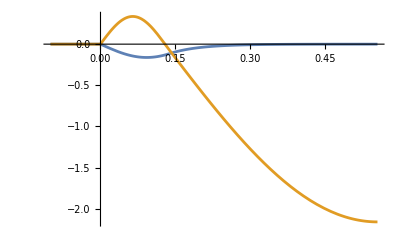
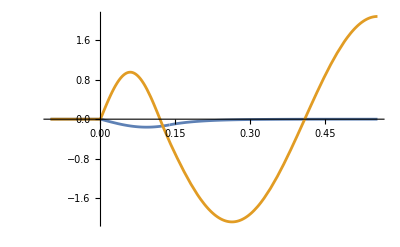
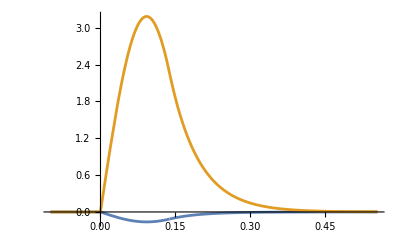
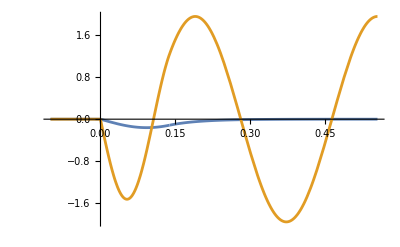
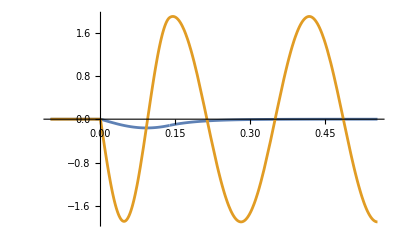
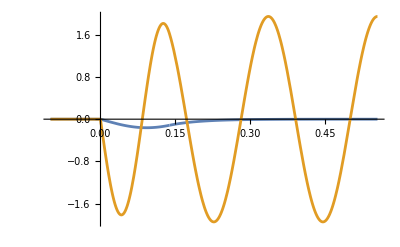
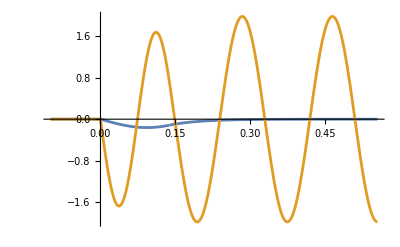
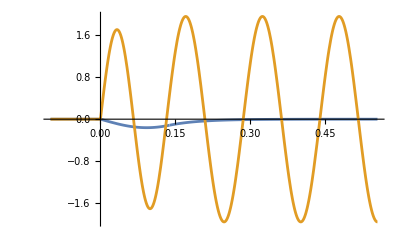

```mathematica
Table[Plot[{fun,Evaluate[funs[[k]]]},{x,-0.1,2tmax},PlotRange->All],{k,Length[funs]}]
```

```mathematica
vals
```

{0.589468,5.03442,-12.4994,12.8302,22.8982,35.803,52.4806,72.4546,94.7457,119.158,146.654,177.564,211.133,246.909,285.498}

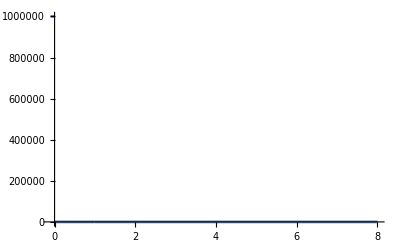

```mathematica
Plot[Piecewise[{{+1000000,x<0},{-1,0<x<am},{0,x>am}}],{x,-0.1,8}]
```